# APPLIED MATH FOR ENGINEERS KANISHK_ASTHANA-CE501-MIDTERM ka112@duke.edu

### Problem 1

1.

```mathematica
x=7;a:=x+2;x=1;
Print["The Value of a is:"]
a
```

The Value of a is:

3

2.

```mathematica
x=2;y=3;z=4;
Print["The Value of a is:"]
a=y^z/x+x/z
```

The Value of a is:

41

3.

```mathematica
Print["The Value is:"]
a=1+Pi
```

The Value is:

1+π

4.

```mathematica
Print["The Value is:"]
1.0+Pi
```

The Value is:

4.14159

5.

```mathematica
Print["The Value is:"]
1.00000000000+Pi
```

The Value is:

4.14159

6.

The function can be defined as follows:

```mathematica
(*Defining Function*)
F[x_]:= Sin[2x]/x;
```

7.

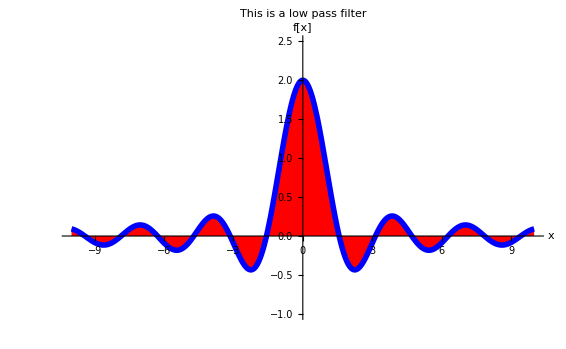

```mathematica
Plot[F[x],{x,-10,10},PlotRange->{-1,2.5},AxesLabel->{"x","f[x]"},PlotLabel->"This is a low pass filter",PlotStyle->{AbsoluteThickness[4],RGBColor[0,0,1]},Filling->Axis,FillingStyle->Red]
```

8.

```mathematica
(*Defining Matrix*)
a={{1,2,4},{2,3,5},{3,4,7}}
Print["The Matrix is Standard Form is:"]
a//MatrixForm(*Standard Form*)
Print["Multiplication with its inverse yeilds an identity matrix:"]
a.Inverse[a]//MatrixForm
Print["The Eigenvectors are:"]
Transpose[N[Eigenvectors[a]]]//MatrixForm
Print["The Eigenvalues are:"]
N[Eigenvalues[a]]
x=Transpose[Eigenvectors[a]];
Print["The Diagnalised Matrix is:"]
Chop[N[Inverse[x].a.x]]//MatrixForm
Print["The operation x^-1.A.x diagnalizes the matrix A where is the eigenvector matrix"]
```

{{1,2,4},{2,3,5},{3,4,7}}

The Matrix is Standard Form is:

(1 | 2 | 4
2 | 3 | 5
3 | 4 | 7)

Multiplication with its inverse yeilds an identity matrix:

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

The Eigenvectors are:

(0.520956 | -2.60515 | 0.884194
0.716733 | 0.0587346 | -2.37547
1. | 1. | 1.)

The Eigenvalues are:

{11.4298,-0.580511,0.150713}

The Diagnalised Matrix is:

(11.4298 | 0 | 0
0 | -0.580511 | 0
0 | 0 | 0.150713)

The operation x^-1.A.x diagnalizes the matrix A where is the eigenvector matrix

### Problem 2

The three methods that can be used to titles,subtitles,sections and subsections etc. are:
1. By generating a horizontal line and clicking on the plus sign and then on other style of text.
2. By clicking on Format then Style and selecting the appropriate action
3. By using the Keyboard Shortcut Alt+Number

### Problem 3

The general solution of the ODE can be found out using by using DSolve as follows:

```mathematica
Clear["Global`*"]
s=DSolve[y'''[x]+y''[x]==3 x^2-Sin[8x],y[x],x];
Print["The General Analytic Solution is (with c1,c2,c3 representing arbitary constants):"]
TraditionalForm[y[x]/.s]
```

The General Analytic Solution is (with c1,c2,c3 representing arbitary constants):

{c_3 x+c_1 ⅇ^-x+c_2+x^4/4-x^3+3 x^2+(sin(8 x))/4160-1/520 cos(8 x)}

### Problem 4

The general solution can be found out using DSolve and the Plotted using the Plot function

The solution of Initial value problem is y[x]:

(ⅇ^-x (-25472+29640 ⅇ^x-25480 ⅇ^x x+12480 ⅇ^x x^2-4160 ⅇ^x x^3+1040 ⅇ^x x^4-8 ⅇ^x Cos[8 x]+ⅇ^x Sin[8 x]))/4160

y'[x] is:

-(ⅇ^-x (-25472+29640 ⅇ^x-25480 ⅇ^x x+12480 ⅇ^x x^2-4160 ⅇ^x x^3+1040 ⅇ^x x^4-8 ⅇ^x Cos[8 x]+ⅇ^x Sin[8 x]))/4160+(ⅇ^-x (4160 ⅇ^x-520 ⅇ^x x+1040 ⅇ^x x^4+65 ⅇ^x Sin[8 x]))/4160

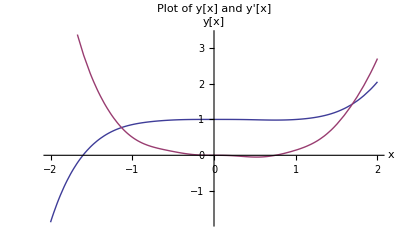

```mathematica
Clear["Global`*"]
sol=DSolve[{y'''[x]+y''[x]==3 x^2-Sin[8x],y[0]==1,y'[0]==0,y''[0]==0},y[x],x];
Print["The solution of Initial value problem is y[x]:"]
s1=y[x]/.sol[[1]]
Print["y'[x] is:"] 
s2=D[s1,x]
Plot[{s1,s2},{x,-2,2},AxesLabel->{"x","y[x]"},PlotLabel->"Plot of y[x] and y'[x]"]
```

The point of intersection can be found out by finding the values of x for which y[x]=y'[x] or y[x]-y'[x]=0
The values of y[x]-y'[x] is as follows:

(ⅇ^-x (-25472+29640 ⅇ^x-25480 ⅇ^x x+12480 ⅇ^x x^2-4160 ⅇ^x x^3+1040 ⅇ^x x^4-8 ⅇ^x Cos[8 x]+ⅇ^x Sin[8 x]))/2080-(ⅇ^-x (4160 ⅇ^x-520 ⅇ^x x+1040 ⅇ^x x^4+65 ⅇ^x Sin[8 x]))/4160

Similarly the plot of y[x]-y'[x] is:

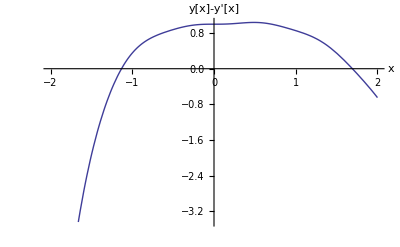

The value of x around 1.5 where the two curves intersect can be found out by finding the series expansion of y[x]-y'[x] about the point 1.5 upto five terms and solving for real values of x for which the series expansion becomes zero:

```mathematica
Print["The point of intersection can be found out by finding the values of x for which y[x]=y'[x] or y[x]-y'[x]=0
The values of y[x]-y'[x] is as follows:"]
sa=s1-s2(*Finding y[x]-y'[x]*)
Print["Similarly the plot of y[x]-y'[x] is:"]

Plot[sa,{x,-2,2},AxesLabel-> {"x","y[x]-y'[x]"}]
Print["The value of x around 1.5 where the two curves intersect can be found out by finding the series expansion of y[x]-y'[x] about the point 1.5 upto five terms and solving for real values of x for which the series expansion becomes zero:"]
```

The series expansion can be found out by using the code below i have stored the value of y[x] in the variable s1 the value of y’[x] in the variable s2 and the value of y[x]-y’[x] in the variable sa.
The series expansion of these variables is:

```mathematica
a=NSolve[Normal[Series[sa,{x,3/2,5}]]==0,x,Reals]
```

{{x→1.69353}}

Storing value of x from above code in variable a1 we get:

```mathematica
Print["The approximate point of intersection of the curves around 1.5 is :"]
a1=x/.a[[1]]
```

The approximate point of intersection of the curves around 1.5 is :

1.69353

Similarly the x coordinate of for point of intersection around -1 can be found out by finding a similar series expansion around the point -1 and storing it in the variable b

```mathematica
b=NSolve[Normal[Series[sa,{x,-1,5}]]==0,x,Reals]
```

{{x→-3.39722},{x→-1.13169},{x→9.8391}}

The second value of b is the closest value to -1 . Extracting solution and storing it in the variable b1 we get:

```mathematica
Print["The approximate point of intersection of the curves around -1 is :"]
b1=x/.b[[2]]
```

The approximate point of intersection of the curves around -1 is :

-1.13169

We can  find the error in our calculation by evaluating the value of y[x]-y’[x] i.e. variable sa at the two values we have obtained and stored in the variables a1 and b1:

```mathematica
Print["The error in calculation for the point near 1.5 is:"]
Limit[sa,x->a1]
Print["The error in calculation for the point near -1 is:"]
Limit[sa,x->b1]
```

The error in calculation for the point near 1.5 is:

-0.0000289059

The error in calculation for the point near -1 is:

-0.0000296336

The same calculations at a precision of 20 can be obtained by changing the WorkingPrecision parameter for the NSolve function.
Storing higher precision values in ap and bp we get the following:

```mathematica
ap=NSolve[Normal[Series[sa,{x,3/2,5}]]==0,x,Reals,WorkingPrecision->20]
```

{{x→1.6935308785422661599}}

Storing higher precision value around 1.5 in variable a1p

```mathematica
Print["The higher precision value is around 1.5 is:"]
a1p=x/.ap[[1]]
```

The higher precision value is around 1.5 is:

1.6935308785422661599

Similarly higher precision value around -1 can be found out as follows:

```mathematica
bp=NSolve[Normal[Series[sa,{x,-1,5}]]==0,x,Reals,WorkingPrecision->20]
```

{{x→-3.3972207737292582876},{x→-1.1316895586134536477},{x→9.8391035470287963065}}

Again the relevant value is the middle term in the array bp. Storing values in b1p we get:

```mathematica
Print["The higher precision value is around -1 is:"]
b1p=x/.bp[[2]]
```

The higher precision value is around -1 is:

-1.1316895586134536477

Similar to lower precision case, we can  find the error in our calculation by evaluating the value of y[x]-y’[x] i.e. variable sa at the two values we have obtained and stored in the variables a1p and b1p:

```mathematica
Print["The error in calculation for the point near 1.5 is:"]
Limit[sa,x->a1p]
Print["The error in calculation for the point near -1 is:"]
Limit[sa,x->b1p]
```

The error in calculation for the point near 1.5 is:

-0.0000289058667191

The error in calculation for the point near -1 is:

-0.0000296336342001

### Problem 5

The ODE (ⅆ^2 y)/(ⅆ x^2)-3yⅆy/ⅆx-y=0 is a NonLinear Ordinary Differential Equation.
Lets check if an analytic solution is available for the initial value problems given y[0]=- 2 and y’[0]=1 , by using mathematica:

```mathematica
DSolve[{y''[x]-3y[x] y'[x]-y[x]==0,y[0]==-2,y'[0]==1},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

Apparently mathematica cannot find the analytic solution lets try to find the Numerical  solution:

```mathematica
solution=NDSolve[{y''[x]-3y[x] y'[x]-y[x]==0,y[0]==-2,y'[0]==1},y[x],{x,-1,1}]
```

NDSolve::ndsz: At x == -0.530857, step size is effectively zero; singularity or stiff system suspected.

{{y[x]→InterpolatingFunction[{{-0.530857,1.}},<>][x]}}

Extracting the Interpolating Function obtained and storing the solution in the variable sol1:

```mathematica
sol1=y[x]/.solution[[1]]
```

InterpolatingFunction[{{-0.530857,1.}},<>][x]

```mathematica
Plot[sol1,{x,-1,1},PlotRange->{-0.9,1},PlotStyle->{AbsoluteThickness[2],RGBColor[0,1,0]},AxesLabel->{"x","y"},PlotLabel-> "Numerical Solution for Problem 5"]
```

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

Solution cannot be displayed for current values of y-> {-0.9,1}.
Therefore to visualize solution using the option PlotRange-> Full  rather than PlotRange->{-0.9,1} :

```mathematica
Plot[sol1,{x,-1,1},PlotRange->Full,PlotStyle->{AbsoluteThickness[2],RGBColor[0,1,0]},AxesLabel->{"x","y"},PlotLabel-> "Numerical Solution for Problem 5"]
```

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

### Problem 6

Short Essay:

During the Keynote addresses of the brothers talked about the history on publishing and the lack of change in it over time. Conrad Wolfram in particular talked about publishers still producing “lifeless documents” even though a lot has changed over the past 300 years. He mentioned the examples of PowerPoint presentations, scientific papers and insurance statements to illustrate his point. His main argument was that, we are not using computational capabilities available to us to convert dead figures into living data even though many of the concepts and information we need to learn is Dynamic. He then argued that by using CDF technology we can convert these life less documents into meaning full living apps that will aid us in our understanding and avoid misunderstandings. He backed his claim by showing examples of a Mathematics textbook, business presentation and pension fund calculator created using CDF technology. Indeed these examples seemed to be more informative than traditional formats and allowed the user greater control over the information, wherein the user could easily recompute the information with different parameteres without the need to do everything all over again. 
I agree with Stephen and Conrad Wolfram’s main point that documents have not evolved with time especially with the advent of the Internet and reduction in cost of publication. CDF technology should be able to bridge resolve that problem by allowing authors to create apps such that their users can understand the concept better. Moreover since these documents are easier to make than flash videos, they eliminate the need for a professional programmer to create these apps . In my own experience I can think of various examples of in Physics,Chemistry and Mathematics which I would have understood better had there been a better way to dynamically visualize the scenario. For example, Kinematics of Moving objects and Rotational Mechanics could have been explained much better with a live demonstration. Many of these demonstrations already exist because of the wolfram demonstrations project. 
 However, I do have minor reservations about the it’s applicability in the Biological Sciences. For example, complex processes like Auditory transduction or Tumor Metastasis have many components that are spatially complex and contain multiple processes; I find it hard to imagine how CDF’s might be helpful in explaining processes such as these (Although I would not trust my own imagination given that I am a new Mathematica user). Nevertheless, I believe overall this is an excellent tool for explaining most everyday problem in feilds like science, business presentations, education etc. . Moreover, Conrad Wolfram’s proposal to use natural language as input to create applications may truly make computing available to everyone without the need to learn a specialized language.

### Problem 7

1. Critique of  Mathematica Demonstration: Flow of Fluid through a Hole in a Tank by Rana Gordji and Sam Gordji (University of Mississippi)
Their code is fine but the problem with their Demonstration is that their solution for fluid flow rate is valid only for the Initial Flow rate for a certain height. Their code does not take care of variation in height as the water level decreases as a function of time. Therefore when the Demonstration is put on Autorun it just shows the changing INITIAL INSTANTANEOUS FLOW RATE for a given height. Therefore it may give the impression that height varies linearly with time while there is NO TIME FACTOR IN THE DEMONSTRATION.

2. Fix:
To fix this problem I have introduced two new variables:
a. Time 
b. Cross Section Area of the Tank
And changed the existing variable Height of Liquid to Initial Height of Liquid.

So everytime the Demonstration is Run the function will recalculate the Solution of:
a. Time varying Differential Equation for height which gives the value of height as a function of Initial Height, Coefficient of Discharge, size of hole, time and cross section of cylinder

DSolve[{y'[t]==-a*c/crosssectionofcylinder*√(2*32.2*y[t]),y[0]==h},y[t],t]
Where y[t] represents the solution to time variation in height, y[0] has been set as initial height variable.
a represents size of hole, c represents coefficient of discharge 32.2 is value of acceleration due to gravity in imperial units
crosssectionofcylinder represents Cross Section of Cylinder.

The Differential Equation was derived as follows:
Volume Flow of Water out hole is give by modified bernoulli equation a*c*√(2 g h) used by the authors.
Therefore in time dt the Volume of water that would flow out is a*c*√(2 g h)dt
Similarly change in Volume of the tank would be: - (Cross section of Tank)*dh
Where dh is change in height 
so 
dh/dt= (a*c*√(2 g h))/(Cross section of Tank)
Solving this equation with the initial value condition h[0]= Initial height we should get time course in change in Height.

b. Radius of Cylinder depending on the Cross section Area Chosen(Assuming Cylindrical Tank).
Radius=√((cross section of cylinder)/π)


c. Recompute the Flow Rate as .
a*c*√(2*32.2*h[t])
Where the height is now a function of time.

I have mentioned what changes I have made in the code by writting comments whereever I have made changes:
Here is the list of changes I have made:
1. Modified Autorun
2. Modified Height of Cylinder to vary with new variable height
3. Introdude Differential Equation
4. Introduced two new variables
5. Recalculated radius of tank for graphic3d
6. Aesthetic changes such a view of slider, autorun
7. Made the Autorun Depend on time
8. Changed the value of Flowrate displayed


The App is as follows:
Please Play with it!

```mathematica
Manipulate[{
he=DSolve[{y'[t]==-a*c/crosssectionofcylinder*√(2*32.2*y[t]),y[0]==h},y[t],t];(*Added to include time variation of height with time*)
height:=Limit[y[t]/.he[[1]],t->time];(*Added to compute value of height at t=time*)
Radius=√(crosssectionofcylinder/π);(* To compute new radius for Graphics3D plot bellow*) 
Graphics3D[{Opacity[0.5],Green,Cylinder[{{.5,.5,0},{.5,.5,height(*Changed*)}},Radius(*Changed*)],Opacity[0.1],Green,Cylinder[{{0.5,.5,0},{.5,.5,10}},Radius(*Changed*)],Opacity[1],Black,Cylinder[{{0,-2,.125},{0,-2.125,.125}},.25]},Axes->True,AxesLabel->{x,y,z},ImageSize->{400,400},PlotLabel->Column[{Row[{"flow (cfs) = ",NumberForm[a*c*√(2*32.2*height(*Changed*)) ,{6,4}]}],Row[{"coordinates of hole: ",{0,-2,0}}]}]]},
{{h,9.0,"initial height of the liquid (ft)"},0.01,10.,Appearance->"Labeled"},{{c,.594,"coefficient of discharge c"},0.1,.80,Appearance->"Labeled"},{{a,.0872,"size of hole (ft^2)"},0.002,.20,Appearance->"Labeled"},{time,0,100, Appearance->"Open"}(*added*),{crosssectionofcylinder,75,750}(*Added*),
AutorunSequencing->{4}(*Changed*),AppearanceElements->All(*Added*)]
```